```mathematica
perp[{a_,b_}]:={-b,a}
```

```mathematica
Solve[{A*x+B*y==v*x-u*y,A*u+B*v==v*x-u*y},{A,B}]
```

{{A→v-y,B→-u+x}}

```mathematica
line[{x_,y_},{u_,v_}]:=line[v-y,x-u,v*x-u*y]
```

```mathematica
project[line[a_,b_,c_],{u_,v_}]:=
{x,y}/.First@Solve[{a*x+b*y==c,-b*x+a*y==-b*u+a*v},{x,y}]
```

```mathematica
intersect[line[a_,b_,c_],line[e_,f_,g_]]:=
{x,y}/.First@Solve[{a*x+b*y==c,e*x+f*y==g},{x,y}]
```

```mathematica
proj[a_,b_,t_]
```

proj[a_,b_,t_]

```mathematica
a={3,10};
b={0,0};
c={8,2};
```

```mathematica
p=(b+c)/2
```

{4,1}

```mathematica
q=p+1/4*perp[c-b]
```

{7/2,3}

```mathematica
s=project[line[b,a],q]
r=project[line[c,a],q]
```

{243/218,405/109}

{1119/178,422/89}

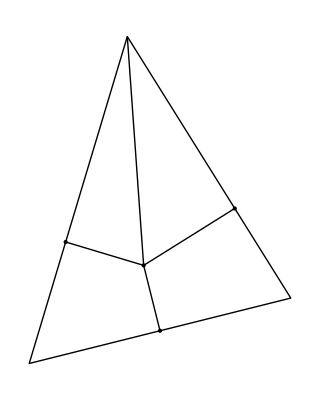

```mathematica
Graphics[{Line[{a,b,c,a}],Point[p],Point[q],Line[{p,q}],Point[s],Point[r],Line[{q,s}], Line[{q,r}],Line[{a,q}]}]
```